```mathematica
boat=ImplicitRegion[y<10.&&y>8./(z^1.2) *x^2.+1./1.3*(z-29.)^2./200.&&0.<z<57.,{x,y,z}]
Region[boat,PlotTheme->"Scientific",AxesLabel->{x,y,z}]
```

ImplicitRegion[y<10.&&y>0.00384615 (-29.+z)^2.+(8. x^2.)/z^1.2&&0.<z<57.,{x,y,z}]

-Graphics3D-

```mathematica
top=ImplicitRegion[57.>z>.5*x^2.&&9.9<=y<18.,{x,y,z}]
Region[top,PlotTheme->"Scientific",AxesLabel->{x,y,z}]
```

ImplicitRegion[57.>z>0.5 x^2.&&9.9≤y<18.,{x,y,z}]

-Graphics3D-

```mathematica
Show[Region[top,PlotTheme->"Scientific",AxesLabel->{x,y,z}],Region[boat,PlotTheme->"Scientific",AxesLabel->{x,y,z}]]
```

-Graphics3D-

```mathematica
Clear[fullBoat];
discreteBoat=DiscretizeRegion[boat];
discreteTop=DiscretizeRegion[top];
(*fullBoat=RegionIntersection[boat,top]*)
(*fullBoatDiscrete=RegionUnion[discreteBoat,discreteTop]
*)
```

This is the boat you want :

```mathematica
boat=ImplicitRegion[y≤ 10.&&y≥ 8./(z^1.2) *x^(2)+1./1.3*(z-29.)^2./200.&&0.≤ z≤ 57.,{x,y,z}]
top=ImplicitRegion[57.>z>.5*x^(1.2)&&9.9<=y<18.,{x,y,z}];
RegionUnion[boat,top]
Region[%]
(*discreteBoat=DiscretizeRegion[boat];
discreteTop=DiscretizeRegion[top];
fullBoatDiscrete=RegionUnion[discreteBoat,discreteTop];
Region[fullBoatDiscrete,PlotTheme->"Scientific",AxesLabel->{x,y,z}]*)
```

ImplicitRegion[y≤10.&&y≥0.00384615 (-29.+z)^2.+(8. x^2)/z^1.2&&0.≤z≤57.,{x,y,z}]

ImplicitRegion[(y≤10.&&y≥0.00384615 (-29.+z)^2.+(8. x^2)/z^1.2&&0.≤z≤57.)||(57.>z>0.5 x^1.2&&9.9≤y<18.),{x,y,z}]

$Aborted[]

ImplicitRegion::bcond: … should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion[fullBoatDiscrete/.{z→5},{x,y,z}]

```mathematica
RegionUnion[boat,top]
```

ImplicitRegion[(y≤10.&&y≥0.00384615 (-29.+z)^2.+(8. x^2.)/z^1.2&&0.≤z≤58.)||(57.>z>0.5 x^2.&&9.9≤y<18.),{x,y,z}]

Region::reg: ImplicitRegion[fullBoatDiscrete/.{z→5},{x,y,z}] is not a correctly specified region.

Region[ImplicitRegion[fullBoatDiscrete/.{z→5},{x,y,z}]]

```mathematica
ztesttop=ImplicitRegion[57.>z>.5*x^2.&&10<=y<18.,{x,y}]
ztestboat=boat=ImplicitRegion[y≤ 10.&&y≥ 8./(z^1.2) *x^(2.)+1./1.3*(z-29.)^2./200.&&0.≤ z≤ 58.,{x,y}]
```

ImplicitRegion[57.>z>0.5 x^2.&&10≤y<18.,{x,y}]

ImplicitRegion[y≤10.&&y≥0.00384615 (-29.+z)^2.+(8. x^2.)/z^1.2&&0.≤z≤58.,{x,y}]

ImplicitRegion[(1. x^2.<110.&&10≤y<18.)||(y≤10.&&y≥2.6+0.0652612 x^2.),{x,y}]

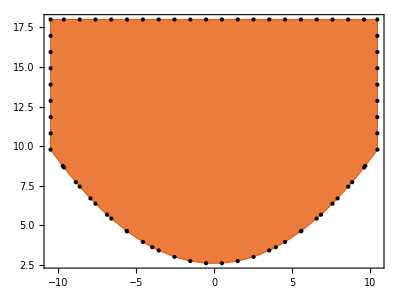

{{-10.6485,10.6485},{2.6,18.}}

```mathematica
ztest=RegionUnion[ztesttop/.{z->55},ztestboat/.{z->55}]
Region[ztest,PlotTheme->"Scientific"]
RegionBounds[ztest]
```

ImplicitRegion[y<10.&&y>0.0025 (-29.+z)^2.+(4. x^2.)/z^1.2,{y,z}]

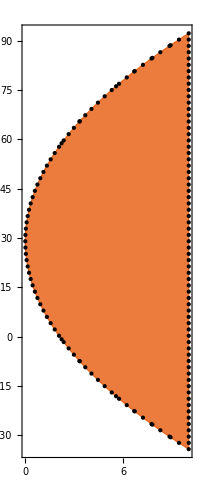

```mathematica
xtestboat=ImplicitRegion[y<10.&&y>4./(z^1.2) *x^2.+.5*(z-29.)^2./200.,{y,z}]
Region[xtestboat/.x->0,PlotTheme->"Scientific"]
```